```mathematica
Clear[pp]
pp[n_,k_]:=pp[n,k]=Sum[ 1/j pp[Floor[n/j],k-1],{j,1,n}]
pp[n_, 0]:=UnitStep[n-1]
ppz[n_, z_,t_]:=Sum[ z^k / (k!)pp[n,k],{k,0,t}]
```

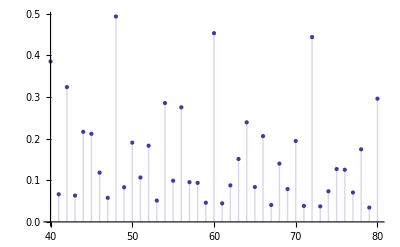

```mathematica
DiscretePlot[ N@ppz[n,1,30]-N@ppz[n-1,1,30],{n,40,80}]
```

```mathematica
Clear[pp]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
pp[n_,k_]:=pp[n,k]=1/j Sum[ pp[n-j,k-1],{j,1,n-1}]
pp[n_,1]:=1/n
pp[n_,0]:=0
pss[n_,z_]:=Sum[ bin[z,k] pp[n,k],{k,0,n}]
psf[n_,z_]:=Sum[ pss[j,z],{j,1,n}]
rootsa[n_]:=If[(c=Exponent[f=psf[n,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
Table[D[pss[10,z],{z,k}]/.z->0,{k,0,12}]
```

{0,3391/151200,33541/453600,949/6720,9563/30240,23/72,49/60,7/24,4/3,0,1,0,0}

```mathematica
Sum[1^k /k! D[pss[10,z],{z,k}]/.z->0,{k,0,12}]
```

1/10

```mathematica
HarmonicNumber[10]
```

7381/2520

```mathematica
Expand@psf[10,z]
```

(184963 z)/129600+(1735487 z^2)/1814400+(226 z^3)/567+(16999 z^4)/145152+(107 z^5)/4320+(23 z^6)/5400+(59 z^7)/120960+z^8/17280+z^9/362880+z^10/3628800

```mathematica
N@rootsa[40]
```

{0.,-8.60779,-8.38004-2.92561 ⅈ,-8.38004+2.92561 ⅈ,-7.70477-5.81542 ⅈ,-7.70477+5.81542 ⅈ,-6.60429-8.63163 ⅈ,-6.60429+8.63163 ⅈ,-5.10743-11.3408 ⅈ,-5.10743+11.3408 ⅈ,-3.50359-13.8299 ⅈ,-3.50359+13.8299 ⅈ,-2.69771-15.5657 ⅈ,-2.69771+15.5657 ⅈ,-2.21913-17.7475 ⅈ,-2.21913+17.7475 ⅈ,-2.18353-11.3591 ⅈ,-2.18353+11.3591 ⅈ,-1.55446-20.0452 ⅈ,-1.55446+20.0452 ⅈ,-1.04005-7.51469 ⅈ,-1.04005+7.51469 ⅈ,-0.815345-22.4795 ⅈ,-0.815345+22.4795 ⅈ,-0.276448-3.72125 ⅈ,-0.276448+3.72125 ⅈ,0.02227-25.0754 ⅈ,0.02227+25.0754 ⅈ,0.971128-27.8583 ⅈ,0.971128+27.8583 ⅈ,2.05107-30.8664 ⅈ,2.05107+30.8664 ⅈ,3.29214-34.1579 ⅈ,3.29214+34.1579 ⅈ,4.744-37.8293 ⅈ,4.744+37.8293 ⅈ,6.50164-42.0671 ⅈ,6.50164+42.0671 ⅈ,8.80847-47.3563 ⅈ,8.80847+47.3563 ⅈ}

```mathematica
pp[10,1]
```

1/10

```mathematica
(* THIS IS https://oeis.org/A089064 - Expansion of Log[1-Log[1-x]]*)
Table[D[pss[n,z],{z,1}]/.z->0,{n,1,10}]
```

{1,0,1/6,1/24,1/15,13/360,97/2520,571/20160,1217/45360,3391/151200}

```mathematica
120/15
```

8

```mathematica
7!
```

5040

```mathematica
97*2
```

194

```mathematica
CoefficientList[Series[Log[1-Log[1-x]],{x,0,10}],x]
```

{0,1,0,1/6,1/24,1/15,13/360,97/2520,571/20160,1217/45360,3391/151200}

```mathematica
CoefficientList[Series[-Log[1-x],{x,0,10}],x]
```

{0,1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
CoefficientList[Series[1/(1-x),{x,0,10}],x]
```

{1,1,1,1,1,1,1,1,1,1,1}

```mathematica
CoefficientList[Expand[(1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9)(1+x^2+x^4+x^6+x^8)(1+x^3+x^6+x^9)(1+x^4+x^8)(1+x^5)(1+x^6)(1+x^7)(1+x^8)(1+x^9)],x]
```

{1,1,2,3,5,7,11,15,22,30,38,51,64,82,101,126,150,182,211,247,284,324,367,409,453,493,537,572,613,643,677,698,718,728,735,735,728,718,698,677,643,613,572,537,493,453,409,367,324,284,247,211,182,150,126,101,82,64,51,38,30,22,15,11,7,5,3,2,1,1}

```mathematica
Table[PartitionsP[n],{n,1,9}]
```

{1,2,3,5,7,11,15,22,30}

```mathematica
Clear[pp]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
pp[n_,r_,k_]:=pp[n,r,k]= Sum[ If[Mod[j,r]≠0,0,1]pp[n-j,r,k-1],{j,1,n-1}]
pp[n_,r_,1]:=If[Mod[n,r]≠0,0,1]
pp[n_,r_,0]:=0
pss[n_,r_,z_]:=Sum[ bin[z,k] pp[n,r,k],{k,0,n}]
psf[n_,r_,z_]:=Sum[ pss[j,r,z],{j,1,n}]
rootsa[n_,r_]:=If[(c=Exponent[f=psf[n,r,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
Table[D[pss[n,1,z]+pss[n,2,z]+pss[n,3,z]+pss[n,4,z]+pss[n,5,z]+pss[n,6,z]+pss[n,7,z]+pss[n,8,z]+pss[n,9,z]+pss[n,10,z],z]/.z->0,{n,1,10}]
```

{1,3/2,4/3,7/4,6/5,2,8/7,15/8,13/9,9/5}

```mathematica
Table[DivisorSigma[1,n]/n,{n,1,10}]
```

{1,3/2,4/3,7/4,6/5,2,8/7,15/8,13/9,9/5}

```mathematica
Table[D[psf[n,1,z]+psf[n,2,z]+psf[n,3,z]+psf[n,4,z]+psf[n,5,z]+psf[n,6,z]+psf[n,7,z]+psf[n,8,z]+psf[n,9,z]+psf[n,10,z],z]/.z->0,{n,1,10}]
```

{1,5/2,23/6,67/12,407/60,527/60,4169/420,9913/840,33379/2520,7583/504}

```mathematica
Sum[ HarmonicNumber[Floor[10/n]],{n,1,10}]
```

7583/504

```mathematica
Sum[ 1,{j,0,6},{k,0,(6-j)/2},{l,0,(6-j-2k)/3},{m,0,(6-j-2k-3l)/4}, {n,0,(6-j-2k-3l-4m)/5}, {o,0,(6-j-2k-3l-4m-5n)/6}]
```

30

```mathematica
Sum[ PartitionsP[j],{j,1,6}]
```

29

```mathematica
Clear[pp]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
pp[n_,r_,k_]:=pp[n,r,k]= Sum[ If[Mod[j,r]≠0,0,1]pp[n-j,r,k-1],{j,1,n-1}]
pp[n_,r_,1]:=If[Mod[n,r]≠0,0,1]
pp[n_,r_,0]:=0
pss[n_,r_,z_]:=Sum[ bin[z,k] pp[n,r,k],{k,0,n}]
psf[n_,r_,z_]:=Sum[ pss[j,r,z],{j,1,n}]
rootsa[n_,r_]:=If[(c=Exponent[f=psf[n,r,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
Clear[lp,p2,pz]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
lp[n_,s_,k_]:=lp[n,s,k]=Sum[ (1-(s+1)^j)/j lp[n-j,s,k-1],{j,1,n-1}]
lp[n_,s_,1]:=(1-(s+1)^n)/n
lp[n_,s_,0]:=If[n==0,1,0]
p2[n_,s_,k_]:=p2[n,k]=Sum[(-s)p2[n-j,s,k-1],{j,1,n-1}]
p2[n_,s_,1]:=-s
p2[n_,s_,0]:=If[n==0,1,0]
pz[n_,s_,z_]:=Sum[ z^k/k! lp[n,s,k],{k,0,n}]
pzx[n_,s_,z_]:=Sum[ bin[z,k] p2[n,s,k],{k,0,n}]
```

```mathematica
Table[lp[n,1,1],{n,1,10}]
```

{-1,-3/2,-7/3,-15/4,-31/5,-21/2,-127/7,-255/8,-511/9,-1023/10}

```mathematica
Table[D[pzx[n,1,z],z]/.z->0,{n,1,10}]
```

{-1,-3/2,-7/3,-15/4,-31/5,-21/2,-127/7,-255/8,-511/9,-1023/10}

```mathematica
Table[(1-2^n)/n,{n,1,10}]
```

{-1,-3/2,-7/3,-15/4,-31/5,-21/2,-127/7,-255/8,-511/9,-1023/10}

```mathematica
Table[D[pzx[n,2,z],z]/.z->0,{n,1,10}]
```

{-2,-4,-26/3,-20,-242/5,-364/3,-2186/7,-820,-19682/9,-29524/5}

```mathematica
Table[-(3^n-1)/n,{n,1,10}]
```

{-2,-4,-26/3,-20,-242/5,-364/3,-2186/7,-820,-19682/9,-29524/5}

```mathematica
FullSimplify[Sum[(1-(1+s)^t)/t,{t,1,n}]]
```

HarmonicNumber[n]+(1+s)^(1+n) LerchPhi[1+s,1,1+n]+Log[-s]

```mathematica
FullSimplify[HarmonicNumber[t]+a^(1+t) LerchPhi[a,1,1+t]+Log[1-a]/.{a->2,t->10}]
```

-118127/504

```mathematica
Table[D[pzx[n,3,z],z]/.z->0,{n,1,10}]
```

{-3,-15/2,-21,-255/4,-1023/5,-1365/2,-16383/7,-65535/8,-29127,-209715/2}

```mathematica
Table[(1-4^n)/n,{n,1,10}]
```

{-3,-15/2,-21,-255/4,-1023/5,-1365/2,-16383/7,-65535/8,-29127,-209715/2}

```mathematica
Table[D[pzx[n,-1,z],z]/.z->0,{n,1,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
Table[(1-0^n)/n,{n,1,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
Table[D[pzx[n,-2,z],z]/.z->0,{n,1,10}]
```

{2,0,2/3,0,2/5,0,2/7,0,2/9,0}

```mathematica
Table[(1-(-1)^n)/n,{n,1,10}]
```

{2,0,2/3,0,2/5,0,2/7,0,2/9,0}

```mathematica
Table[D[pzx[n,-3,z],z]/.z->0,{n,1,10}]
```

{3,-3/2,3,-15/4,33/5,-21/2,129/7,-255/8,57,-1023/10}

```mathematica
Table[(1-(-2)^n)/n,{n,1,10}]
```

{3,-3/2,3,-15/4,33/5,-21/2,129/7,-255/8,57,-1023/10}

```mathematica
Table[FullSimplify@pz[n,1,z],{n,0,6}]//TableForm
```

1
-z
1/2 (-3+z) z
-1/6 (-7+z) (-2+z) z
1/24 (-5+z) z (18+(-13+z) z)
-1/120 (-4+z) z (-186+z (171+(-26+z) z))
1/720 (-7+z) z (1080+(-11+z) z (122+(-27+z) z))

```mathematica
Sum[pzx[j,-1,2],{j,0,10}]
```

66

```mathematica
Pochhammer[3,10]/(10!)
```

66

```mathematica
Table[Expand@Sum[pz[j,-1,z],{j,0,n}],{n,0,6}]//TableForm
```

1
1+z
1+(3 z)/2+z^2/2
1+(11 z)/6+z^2+z^3/6
1+(25 z)/12+(35 z^2)/24+(5 z^3)/12+z^4/24
1+(137 z)/60+(15 z^2)/8+(17 z^3)/24+z^4/8+z^5/120
1+(49 z)/20+(203 z^2)/90+(49 z^3)/48+(35 z^4)/144+(7 z^5)/240+z^6/720

```mathematica
Table[FullSimplify@pz[n,-2,z+1],{n,0,6}]//TableForm
```

1
2 (1+z)
2 (1+z)^2
2/3 (1+z) (3+2 z (2+z))
2/3 (1+z)^2 (2+(1+z)^2)
2/15 (1+z) (15+2 z (2+z) (7+z (2+z)))
2/45 (1+z)^2 (45+2 z (2+z) (12+z (2+z)))

```mathematica
zp[z_,n_,s_]:= Product[((-s)z+(-s)j),{j,0,n-1}]/n!
```

```mathematica
Table[ FullSimplify[zp[z,n,-2]],{n,0,5}]//TableForm
```

1
2 z
2 z (1+z)
4/3 z (1+z) (2+z)
2/3 z (1+z) (2+z) (3+z)
4/15 z (1+z) (2+z) (3+z) (4+z)

```mathematica
Sum[ 1,{j,0,5}]
```

6

```mathematica
FullSimplify@Sum[2^j/j,{j,1,n}]
```

-ⅈ π-2^(1+n) LerchPhi[2,1,1+n]

```mathematica
Sum[(-s)(-s),{j,1,10-1}]
```

9 s^2

```mathematica
p2[10,s,2]
```

9 s^2

```mathematica
p2[10,s,1]
```

-s

```mathematica
Table[ p2[n,s,k],{k,1,6},{n,1,10}]//TableForm
```

-s | -s | -s | -s | -s | -s | -s | -s | -s | -s
0 | s^2 | 2 s^2 | 3 s^2 | 4 s^2 | 5 s^2 | 6 s^2 | 7 s^2 | 8 s^2 | 9 s^2
0 | 0 | -s^3 | -3 s^3 | -6 s^3 | -10 s^3 | -15 s^3 | -21 s^3 | -28 s^3 | -36 s^3
0 | 0 | 0 | s^4 | 4 s^4 | 10 s^4 | 20 s^4 | 35 s^4 | 56 s^4 | 84 s^4
0 | 0 | 0 | 0 | -s^5 | -5 s^5 | -15 s^5 | -35 s^5 | -70 s^5 | -126 s^5
0 | 0 | 0 | 0 | 0 | s^6 | 6 s^6 | 21 s^6 | 56 s^6 | 126 s^6

```mathematica
Table[ s^2 Pochhammer[k-1,1]/1!,{k,1,10}]
```

{0,s^2,2 s^2,3 s^2,4 s^2,5 s^2,6 s^2,7 s^2,8 s^2,9 s^2}

```mathematica
Table[ -s^3 Pochhammer[k-2,2]/2!,{k,1,10}]
```

{0,0,-s^3,-3 s^3,-6 s^3,-10 s^3,-15 s^3,-21 s^3,-28 s^3,-36 s^3}

```mathematica
Table[ s^4 Pochhammer[k-3,3]/3!,{k,1,10}]
```

{0,0,0,s^4,4 s^4,10 s^4,20 s^4,35 s^4,56 s^4,84 s^4}

```mathematica
Table[ (-s)^k Pochhammer[n-k+1,k-1]/(k-1)!,{k,1,6},{n,1,10}]//TableForm
```

-s | -s | -s | -s | -s | -s | -s | -s | -s | -s
0 | s^2 | 2 s^2 | 3 s^2 | 4 s^2 | 5 s^2 | 6 s^2 | 7 s^2 | 8 s^2 | 9 s^2
0 | 0 | -s^3 | -3 s^3 | -6 s^3 | -10 s^3 | -15 s^3 | -21 s^3 | -28 s^3 | -36 s^3
0 | 0 | 0 | s^4 | 4 s^4 | 10 s^4 | 20 s^4 | 35 s^4 | 56 s^4 | 84 s^4
0 | 0 | 0 | 0 | -s^5 | -5 s^5 | -15 s^5 | -35 s^5 | -70 s^5 | -126 s^5
0 | 0 | 0 | 0 | 0 | s^6 | 6 s^6 | 21 s^6 | 56 s^6 | 126 s^6

```mathematica
FullSimplify[Sum[ (-s)^k Pochhammer[n-k+1,k-1]/(k-1)!,{n,1,10}]]
```

-((-11+k) (966240+(-11+k) k (97416+(-11+k) k (4708+(-11+k) k (110+(-11+k) k)))) (-s)^k)/(Gamma[11-k] Gamma[k])

```mathematica
Expand@Sum[Binomial[z,k] (-s)^k Pochhammer[n-k+1,k-1]/(k-1)!,{k,0,Infinity}]
```

-s z Hypergeometric2F1[1-n,1-z,2,-s]

```mathematica
pzn[n_,s_,z_]:=-s z Hypergeometric2F1[1-n,1-z,2,-s]
```

```mathematica
Sum[-s z Hypergeometric2F1[1-n,1-z,2,-s],{n,1,m}]/.s->-1
```

z ((-1+0^z)/z+DifferenceRoot[Function[{y,n},{(n+z) y[n]+(-1-2 n-z) y[1+n]+(1+n) y[2+n]==0,y[0]==0,y[1]==-(-1+0^z)/z,y[2]==1-(-1+0^z)/z}]][1+m])

```mathematica
FullSimplify[Sum[ (s)^k Binomial[-n-k+1,k-1],{n,1,m}]]
```

(s^k (-(-1+k) Binomial[-k,-1+k]+(-1+k+m) Binomial[-k-m,-1+k]))/k

```mathematica
(-s)^k Pochhammer[n-k+1,k-1]/(k-1)!/.{n->10,s->5,k->4}
```

52500

```mathematica
p2[10,5,4]
```

52500

```mathematica
- (s)^k Binomial[-(n-k+1),k-1]/.{n->10,s->5,k->4}
```

52500

```mathematica
(-1)^k (-1)^(k-1)
```

(-1)^(-1+2 k)

```mathematica
(-1)^(-1)
```

-1

```mathematica
Sum[ - (s)^k Binomial[-(n-k+1),k-1],{n,1,m}]
```

```mathematica
((-1+k-m) s^k Binomial[-2+k-m,-1+k])/k/.{m->10,s->5,k->4}
```

131250

```mathematica
st[m_, s_, k_] := ((-1+k-m) s^k Binomial[-2+k-m,-1+k])/k
s3[m_, s_, k_] := ((-1+k-m) s^k (-1)^(k-1)Pochhammer[-(-2+k-m),-1+k])/(k!)
s4[m_, s_, k_] := ((m-k+1) (-s)^k Pochhammer[m-k+2,k-1])/(k!)
s5[n_,s_,k_]:=s^k Pochhammer[-n,k]/k!
s2[n_, s_, k_] := Sum[ p2[j,s,k],{j,1,n}]
```

```mathematica
Table[ s5[n,s,1]-s2[n,s,1],{n,2,8},{s,-2,3}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
((m-k+1) (-s)^k Pochhammer[m-k+2,k-1])/(k!)/.m->n
```

```mathematica
Expand@Table[ ((1-k+n) (-s)^k Pochhammer[2-k+n,-1+k])/(k!),{k,0,6}]//TableForm
```

1
-n s
-(n s^2)/2+(n^2 s^2)/2
-(n s^3)/3+(n^2 s^3)/2-(n^3 s^3)/6
-(n s^4)/4+(11 n^2 s^4)/24-(n^3 s^4)/4+(n^4 s^4)/24
-(n s^5)/5+(5 n^2 s^5)/12-(7 n^3 s^5)/24+(n^4 s^5)/12-(n^5 s^5)/120
-(n s^6)/6+(137 n^2 s^6)/360-(5 n^3 s^6)/16+(17 n^4 s^6)/144-(n^5 s^6)/48+(n^6 s^6)/720

```mathematica
Expand@Table[s^k Pochhammer[-n,k]/k!,{k,0,6}]//TableForm
```

1
-n s
-(n s^2)/2+(n^2 s^2)/2
-(n s^3)/3+(n^2 s^3)/2-(n^3 s^3)/6
-(n s^4)/4+(11 n^2 s^4)/24-(n^3 s^4)/4+(n^4 s^4)/24
-(n s^5)/5+(5 n^2 s^5)/12-(7 n^3 s^5)/24+(n^4 s^5)/12-(n^5 s^5)/120
-(n s^6)/6+(137 n^2 s^6)/360-(5 n^3 s^6)/16+(17 n^4 s^6)/144-(n^5 s^6)/48+(n^6 s^6)/720

```mathematica
s5[n_,s_,k_]:=s^k Pochhammer[-n,k]/k!
```

```mathematica
Sum[ p2[j,3,4],{j,1,12}]
```

40095

```mathematica
3^4 Pochhammer[-12,4]/4!
```

40095

```mathematica
Sum[ Binomial[z,k] s^k Pochhammer[-n,k]/k!,{k,0,Infinity}]
```

Hypergeometric2F1[-n,-z,1,-s]

```mathematica
Table[ Hypergeometric2F1[-n,-z,1,-s]/.{z->1,s->-1},{n,1,12}]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
Sum[pz[j,-3,-3],{j,1,15}]
```

-9248769

```mathematica
Table[Sum[pz[j,-1,1],{j,1,n}],{n,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[ FullSimplify[Sum[ (-1)^(k-j) Binomial[k,j]  Hypergeometric2F1[-n,-j,1,-s],{j,0,k}]],{k,1,5}]//TableForm
```

-n s
1/2 (-1+n) n s^2
-1/6 (-2+n) (-1+n) n s^3
1/24 (-3+n) (-2+n) (-1+n) n s^4
-1/120 (-4+n) (-3+n) (-2+n) (-1+n) n s^5

```mathematica
N@D[Hypergeometric2F1[-n,-z,1,-s],z]/.{z->0,n->10,s->-1}
```

2.92897

```mathematica
HarmonicNumber[10.]
```

2.92897

```mathematica
Hypergeometric2F1[-n,-z,1,-s]/.{z->5,n->10,s->-1}
```

3003

```mathematica
Pochhammer[5+1,10]/(10!)
```

3003

```mathematica
Pochhammer[10+1,5]/(5!)
```

3003

```mathematica
Sum[ Binomial[z,k](-1)^k Pochhammer[-n,k]/k!,{k,0,Infinity}]
```

Gamma[1+n+z]/(Gamma[1+n] Gamma[1+z])

```mathematica
Hypergeometric2F1[-n,-z,1,1]/.{n->7,z->9}
```

11440

```mathematica
Pochhammer[9+1,7]/7!
```

11440

```mathematica
Integrate[ 1,{j,0,n},{k,0,n-j}]
```

n^2/2

```mathematica
Integrate[ 1,{j,0,n},{k,0,n-j},{l,0,n-j-k}]
```

n^3/6

```mathematica
Integrate[ 1,{j,0,n},{k,0,n-j},{l,0,n-j-k},{m,0,n-j-k-l}]
```

n^4/24

```mathematica
Sum[ Binomial[z,k] n^k/k!,{k,0,Infinity}]
```

Hypergeometric1F1[-z,1,-n]

```mathematica
Integrate[ (-s)(-s),{j,0,n},{k,0,n-j}]
```

(n^2 s^2)/2

```mathematica
Integrate[ (-s)(-s)(-s),{j,0,n},{k,0,n-j},{l,0,n-j-k}]
```

-1/6 n^3 s^3

```mathematica
Sum[ Binomial[z,k] (-s)^k n^k/k!,{k,0,Infinity}]
```

Hypergeometric1F1[-z,1,n s]

```mathematica
Sum[Binomial[z,k](1/(1-x)-1)^k,{k,0,Infinity}]
```

(-1/(-1+x))^z

```mathematica
Limit[(1-x^m)/(1-x),x->1]
```

m

```mathematica
Series[(2/(1-x))^2,{x,0,10}]
```

4+8 x+12 x^2+16 x^3+20 x^4+24 x^5+28 x^6+32 x^7+36 x^8+40 x^9+44 x^10+O[x]^11

```mathematica
Sum[ Binomial[z,k](2/(1-x)-1)^k,{k,0,Infinity}]
```

2^z (-1/(-1+x))^z

```mathematica
FullSimplify@Sum[Binomial[z,k](2/(1-x)-1)^k,{k,0,n}]
```

2^z (1/(1-x))^z+((1+x) ((1+x)/(1-x))^n Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,(1+x)/(-1+x)])/(-1+x)

```mathematica
Limit[2^z (1/(1-x))^z+((1+x) ((1+x)/(1-x))^n Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,(1+x)/(-1+x)])/(-1+x),x->1]
```

Limit[2^z (1/(1-x))^z+((1+x) ((1+x)/(1-x))^n Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,(1+x)/(-1+x)])/(-1+x),x→1]

```mathematica
FullSimplify@Sum[Binomial[z,k]((-s)/(1-x)-1)^k,{k,0,n}]
```

(s/(-1+x))^z-(1+s-x)^(1+n) (-1+x)^(-1-n) Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,1-s/(-1+x)]

```mathematica
Limit[(s/(-1+x))^z-(1+s-x)^(1+n) (-1+x)^(-1-n) Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,1-s/(-1+x)],x->1]
```

Limit[(s/(-1+x))^z-(1+s-x)^(1+n) (-1+x)^(-1-n) Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,1-s/(-1+x)],x→1]

```mathematica
Clear[lpt,p2t,pzt]
t[n_, a_, b_] := b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
lpt[n_,s_,a_,b_,k_]:=lpt[n,s,a,b,k]=Sum[ (1-(s+1)^j)/j lpt[n-j,s,a,b,k-1],{j,1,n-1}]-a Sum[ (1-(s+1)^j)/j lpt[n-j,s,a,b,k-1],{j,a,n-1,a}]
lpt[n_,s_,a_,b_,1]:=t[n,a,b](1-(s+1)^n)/n
lpt[n_,s_,a_,b_,0]:=If[n==0,1,0]
p2t[n_,s_,a_,b_,k_]:=p2t[n,s,a,b,k]=Sum[(-s)p2t[n-j,s,a,b,k-1],{j,1,n-1}]
p2t[n_,s_,a_,b_,1]:=-s
p2t[n_,s_,a_,b_,0]:=If[n==0,1,0]
pzt[n_,s_,a_,b_,z_]:=Sum[ z^k/k! lpt[n,s,a,b,k],{k,0,n}]
pzxt[n_,s_,a_,b_,z_]:=Sum[ bin[z,k] p2t[n,s,a,b,k],{k,0,n}]
```

```mathematica
Table[pzt[k,-1,2,1,n],{n,0,6},{k,0,n}]//TableForm
```

Power::indet: Indeterminate expression 0^0 encountered.

Indeterminate |  |  |  |  |  | 
1 | 1 |  |  |  |  | 
1 | 2 | 1 |  |  |  | 
1 | 3 | 3 | 1 |  |  | 
1 | 4 | 6 | 4 | 1 |  | 
1 | 5 | 10 | 10 | 5 | 1 | 
1 | 6 | 15 | 20 | 15 | 6 | 1

```mathematica
tbs[t_, n_] := Table[ ff[z+1,n-m k]ff[-z,k], {m,1,t},{k,0,n/m}]//TableForm
tbs2[t_, n_] := Table[ ff[z+1,n-m k]ff[-z,k], {k,1,t},{m,1,t/k}]//TableForm
```

```mathematica
tbs[10,12]
```

ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,11] | ff[-z,2] ff[1+z,10] | ff[-z,3] ff[1+z,9] | ff[-z,4] ff[1+z,8] | ff[-z,5] ff[1+z,7] | ff[-z,6] ff[1+z,6] | ff[-z,7] ff[1+z,5] | ff[-z,8] ff[1+z,4] | ff[-z,9] ff[1+z,3] | ff[-z,10] ff[1+z,2] | ff[-z,11] ff[1+z,1] | ff[-z,12] ff[1+z,0]
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,10] | ff[-z,2] ff[1+z,8] | ff[-z,3] ff[1+z,6] | ff[-z,4] ff[1+z,4] | ff[-z,5] ff[1+z,2] | ff[-z,6] ff[1+z,0] |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,9] | ff[-z,2] ff[1+z,6] | ff[-z,3] ff[1+z,3] | ff[-z,4] ff[1+z,0] |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,8] | ff[-z,2] ff[1+z,4] | ff[-z,3] ff[1+z,0] |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,7] | ff[-z,2] ff[1+z,2] |  |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,6] | ff[-z,2] ff[1+z,0] |  |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,5] |  |  |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,4] |  |  |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,3] |  |  |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,12] | ff[-z,1] ff[1+z,2] |  |  |  |  |  |  |  |  |  |  |

```mathematica
tbs[14,9]
```

ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,8] | ff[-z,2] ff[1+z,7] | ff[-z,3] ff[1+z,6] | ff[-z,4] ff[1+z,5] | ff[-z,5] ff[1+z,4] | ff[-z,6] ff[1+z,3] | ff[-z,7] ff[1+z,2] | ff[-z,8] ff[1+z,1] | ff[-z,9] ff[1+z,0]
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,7] | ff[-z,2] ff[1+z,5] | ff[-z,3] ff[1+z,3] | ff[-z,4] ff[1+z,1] |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,6] | ff[-z,2] ff[1+z,3] | ff[-z,3] ff[1+z,0] |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,5] | ff[-z,2] ff[1+z,1] |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,4] |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,3] |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,2] |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,1] |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] | ff[-z,1] ff[1+z,0] |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] |  |  |  |  |  |  |  |  | 
ff[-z,0] ff[1+z,9] |  |  |  |  |  |  |  |  |

```mathematica
Sum[(-1)^k  Binomial[-z,k],{k,1,n,3}]
```

3^(-1-z) (0^-z-(-1)^(1/3) (1+(-1)^(1/3))^z+(-1)^(2/3) (1-(-1)^(2/3))^z+(-1)^n 3^(1+z) Binomial[-z,3+n] HypergeometricPFQ[{1,1+n/3+z/3,4/3+n/3+z/3,5/3+n/3+z/3},{4/3+n/3,5/3+n/3,2+n/3},1])

```mathematica
Limit[Sum[Pochhammer[z+1,k]/k!,{k,0,n,3}],z->0]
```

Limit[(3^(-1-z) ((-(1+(-1)^(1/3))^z+(-1)^(2/3) (1-(-1)^(2/3))^z+0^(-1-z) 3^z (-1+(-1)^(2/3))) Gamma[4+n] Gamma[1+z]-3^(1+z) (-1+(-1)^(2/3)) Gamma[4+n+z] HypergeometricPFQ[{1,4/3+n/3+z/3,5/3+n/3+z/3,2+n/3+z/3},{4/3+n/3,5/3+n/3,2+n/3},1]))/((-1+(-1)^(2/3)) Gamma[4+n] Gamma[1+z]),z→0]

```mathematica
Table[ Pochhammer[-3,k]/k!,{k,0,5}]
```

{1,-3,3,-1,0,0}

```mathematica
CoefficientList[Series[(1/(1-x))^(-5/3),{x,0,4}],x]
```

{1,-5/3,5/9,5/81,5/243}

```mathematica
CoefficientList[Series[(1+x+x^2+x^3+x^4)^(-5/3),{x,0,4}],x]
```

{1,-5/3,5/9,5/81,5/243}

```mathematica
Sum[ Pochhammer[k,2]/2! x^k,{k,0,Infinity}]
```

-x/(-1+x)^3

```mathematica
Sum[ Pochhammer[k,3]/3! x^k,{k,0,Infinity}]
```

x/(-1+x)^4

```mathematica
Sum[ Pochhammer[k,4]/4! x^k,{k,0,Infinity}]
```

-x/(-1+x)^5

```mathematica
Sum[Binomial[k,3] x^k,{k,0,Infinity}]
```

x^3/(-1+x)^4

```mathematica
Sum[Binomial[k,5] x^k,{k,0,Infinity}]
```

x^5/(-1+x)^6

```mathematica
Sum[ Pochhammer[k,4]/4! x^k,{k,0,Infinity}]
```

-x/(-1+x)^5

```mathematica
Sum[x^(4k),{k,0,Infinity}]
```

1/(1-x^4)

```mathematica
CoefficientList[Series[ 1/(1-x)^2,{x,0,10}],x]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
CoefficientList[Series[ 1/(1-x)^3,{x,0,10}],x]
```

{1,3,6,10,15,21,28,36,45,55,66}

```mathematica
Sum[Binomial[k,2] x^k,{k,0,Infinity}]
```

-x^2/(-1+x)^3

```mathematica
CoefficientList[Series[-x^2/(-1+x)^3,{x,0,10}],x]
```

{0,0,1,3,6,10,15,21,28,36,45}

```mathematica
FullSimplify[Sum[1,{j,0,n},{k,0,n-j},{l,0,n-j-k}]]
```

1/6 (1+n) (2+n) (3+n)

```mathematica
FullSimplify[Sum[1,{j,1,n-2},{k,1,n-j-1},{l,1,n-j-k}]]
```

1/6 (-2+n) (-1+n) n

```mathematica
FullSimplify[Sum[1,{j,0,n},{k,0,n-j},{l,0,n-j-k},{m,0,n-j-k-l}]]
```

1/24 (1+n) (2+n) (3+n) (4+n)

```mathematica
FullSimplify[Sum[1,{j,1,n-3},{k,1,n-j-2},{l,1,n-j-k-1},{m,1,n-j-k-l}]]
```

1/24 (-3+n) (-2+n) (-1+n) n

```mathematica
Table[D[Binomial[n,k],{k,2}]/.k->0,{n,1,10}]
```

{2-π^2/3,7/2-π^2/3,85/18-π^2/3,415/72-π^2/3,12019/1800-π^2/3,13489/1800-π^2/3,726301/88200-π^2/3,3144919/352800-π^2/3,30300391/3175200-π^2/3,32160403/3175200-π^2/3}

```mathematica
HarmonicNumber[10]
```

7381/2520

```mathematica
Table[D[Pochhammer[z+1,k],{z,2}]/k!/.z->0,{k,1,10}]
```

{0,1,2,35/12,15/4,203/45,469/90,29531/5040,6515/1008,177133/25200}

```mathematica
FullSimplify[Sum[1,{j,2,n-4},{k,2,n-j-2},{l,2,n-j-k}]]
```

1/6 (-5+n) (-4+n) (-3+n)

```mathematica
FullSimplify[Sum[1,{j,2,n-6},{k,2,n-j-4},{l,2,n-j-k-2},{m,2,n-j-k-l}]]
```

1/24 (-7+n) (-6+n) (-5+n) (-4+n)

```mathematica
FullSimplify[Sum[1,{j,-1,n+2},{k,-1,n-j+1},{l,-1,n-j-k}]]
```

1/6 (4+n) (5+n) (6+n)

```mathematica
Table[ Pochhammer[n+1-k y,k]/k!,{y,-2,2}]/.k->3//TableForm
```

1/6 (7+n) (8+n) (9+n)
1/6 (4+n) (5+n) (6+n)
1/6 (1+n) (2+n) (3+n)
1/6 (-2+n) (-1+n) n
1/6 (-5+n) (-4+n) (-3+n)

```mathematica
FullSimplify[Table[ Pochhammer[n+1-k y,k]/k! - Pochhammer[n-k y,k]/k!,{y,-2,2}]/.k->3//TableForm]
```

1/2 (7+n) (8+n)
1/2 (4+n) (5+n)
1/2 (1+n) (2+n)
1/2 (-2+n) (-1+n)
1/2 (-5+n) (-4+n)

```mathematica
Table[ Pochhammer[n+1-k y,k-1]/(k-1)!,{y,-2,2}]/.k->3//TableForm
```

1/2 (7+n) (8+n)
1/2 (4+n) (5+n)
1/2 (1+n) (2+n)
1/2 (-2+n) (-1+n)
1/2 (-5+n) (-4+n)

```mathematica
FullSimplify[Table[ Pochhammer[n+1-k y,k]/k! - Pochhammer[n-k y,k]/k!,{y,-2,2}]/.k->4//TableForm]
```

1/6 (9+n) (10+n) (11+n)
1/6 (5+n) (6+n) (7+n)
1/6 (1+n) (2+n) (3+n)
1/6 (-3+n) (-2+n) (-1+n)
1/6 (-7+n) (-6+n) (-5+n)

```mathematica
Table[ Pochhammer[n+1-k y,k-1]/(k-1)!,{y,-2,2}]/.k->4//TableForm
```

1/6 (9+n) (10+n) (11+n)
1/6 (5+n) (6+n) (7+n)
1/6 (1+n) (2+n) (3+n)
1/6 (-3+n) (-2+n) (-1+n)
1/6 (-7+n) (-6+n) (-5+n)

```mathematica
Expand[(k/(k-1))(k-1) y]
```

k y

```mathematica
FullSimplify[Sum[1,{j,0,n/2},{k,0,(n-2j)/2},{l,0,(n-2j-2k)/2}]]
```

1/48 (2+n) (4+n) (6+n)

```mathematica
FullSimplify[Sum[1,{j,0,n},{k,0,(n-j)},{l,0,(n-j-k)}]]
```

1/6 (1+n) (2+n) (3+n)

```mathematica
FullSimplify[Sum[1,{j,0,n/3},{k,0,(n-3j)/3},{l,0,(n-3j-3k)/3}]]
```

1/162 (3+n) (6+n) (9+n)

```mathematica
FullSimplify[Sum[1,{j,0,n/4},{k,0,(n-4j)/4},{l,0,(n-4j-4k)/4}]]
```

1/384 (4+n) (8+n) (12+n)

```mathematica
48/6
```

8

```mathematica
162/6
```

27

```mathematica
384/6
```

64

```mathematica
Sum[1,{j,0,n},{k,0,n-j}]
```

1/2 (1+n) (2+n)

```mathematica
Limit[Sum[1/(a^2),{j,0,a n},{k,0,a n-j}],a->Infinity]
```

n^2/2

```mathematica
Limit[Sum[1/(a^3),{j,0,a n},{k,0,a n-j},{l,0,a n-j-k}],a->Infinity]
```

n^3/6

```mathematica
Limit[Sum[1/(a^2),{j,1,a n-1},{k,1,a n-j}],a->Infinity]
```

n^2/2

```mathematica
Limit[Sum[1/(a^3),{j,1,a n-2},{k,1,a n-j-1},{l,1,a n-j-k}],a->Infinity]
```

n^3/6

```mathematica
ba[n_,k_]:=Sum[  Binomial[k,j] n^j/(j!),{j,0,k}]
```

```mathematica
Table[Expand[ba[n,k]],{k,0,8}]//TableForm
```

1
1+n
1+2 n+n^2/2
1+3 n+(3 n^2)/2+n^3/6
1+4 n+3 n^2+(2 n^3)/3+n^4/24
1+5 n+5 n^2+(5 n^3)/3+(5 n^4)/24+n^5/120
1+6 n+(15 n^2)/2+(10 n^3)/3+(5 n^4)/8+n^5/20+n^6/720
1+7 n+(21 n^2)/2+(35 n^3)/6+(35 n^4)/24+(7 n^5)/40+(7 n^6)/720+n^7/5040
1+8 n+14 n^2+(28 n^3)/3+(35 n^4)/12+(7 n^5)/15+(7 n^6)/180+n^7/630+n^8/40320

```mathematica
Expand[Limit[Sum[1/(a^2),{j,1,a n},{k,a,a n-j}],a->Infinity]-Limit[Sum[1/(a),{j,1,a n}],a->Infinity]+1]
```

1-2 n+n^2/2

```mathematica
Limit[Sum[1/(a),{j,1,a n}],a->Infinity]
```

n

```mathematica
Sum[  Binomial[z,j] n^j/(j!),{j,0,Infinity}]
```

Hypergeometric1F1[-z,1,-n]

```mathematica
FullSimplify[Sum[1/(a^1),{j,1,a n}]]/.a->x
FullSimplify[Sum[1/(a^2),{j,1,a n-1},{k,1,a n-j}]]/.a->x
FullSimplify[Sum[1/(a^3),{j,1,a n-2},{k,1,a n-j-1},{l,1,a n-j-k}]]/.a->x
FullSimplify[Sum[1/(a^4),{j,1,a n-3},{k,1,a n-j-2},{l,1,a n-j-k-1},{m,1,a n-j-k-l}]]/.a->x
```

n

(n (-1+n x))/(2 x)

(n (-2+n x) (-1+n x))/(6 x^2)

(n (-3+n x) (-2+n x) (-1+n x))/(24 x^3)

```mathematica
pr[n_,k_,x_]:= Product[(n x-j),{j,0,k-1}]/( k! x^k)
```

```mathematica
Table[pr[n,k,x],{k,1,4}]//TableForm
```

n
(n (-1+n x))/(2 x)
(n (-2+n x) (-1+n x))/(6 x^2)
(n (-3+n x) (-2+n x) (-1+n x))/(24 x^3)

```mathematica
Limit[(n (-3+n x) (-2+n x) (-1+n x))/(24 x^3),x->Infinity]
```

n^4/24

```mathematica
Sum[(-1)^(j+1)/j  n^j/(j!),{j,1,Infinity}]
```

EulerGamma+Gamma[0,n]+Log[n]

```mathematica
FullSimplify[D[(n (-1+n x))/(2 x),x]]
```

n/(2 x^2)

```mathematica
FullSimplify[D[(n (-2+n x) (-1+n x))/(6 x^2),x]]
```

(n (-4+3 n x))/(6 x^3)

```mathematica
FullSimplify[D[(n (-3+n x) (-2+n x) (-1+n x))/(24 x^3),x]]
```

(n (9+n x (-11+3 n x)))/(12 x^4)

```mathematica
Sum[ Binomial[z,k]x^k Product[(n /x-j),{j,0,k-1}]/( k! ),{k,0,Infinity}]
```

Hypergeometric2F1[-n/x,-z,1,x]

```mathematica
Limit[Hypergeometric2F1[-n/x,-z,1,x],x->0]
```

Limit[Hypergeometric2F1[-n/x,-z,1,x],x→0]

```mathematica
D[Hypergeometric2F1[-n/x,-z,1,x],x]
```

(n z Hypergeometric2F1[1-n/x,1-z,2,x])/x+(n Hypergeometric2F1^(1,0,0,0)[-n/x,-z,1,x])/x^2

```mathematica
Series[(1-x)/(1-x^2),{x,0,10}]
```

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10+O[x]^11

```mathematica
Series[(1-x)/(1-x^2),{x,0,10}]
```